## ^183Au - Positive Parity

```mathematica
x1n=Table[N[i],{i,19/2,51/2,2}];
y1n={1056,1488,1987,2540,3148,3796,4457,5133,5912};
t1n=Table[{x1n[[i]],y1n[[i]]},{i,1,Length[x1n]}];
```

```mathematica
x2n=Table[N[i],{i,9/2,53/2,2}];
y2n=Reverse[{6242,5497,4760,4050,3358,2690,2063,1492,990,566,232,12.78}];
t2n=Table[{x2n[[i]],y2n[[i]]},{i,1,Length[x2n]}];
```

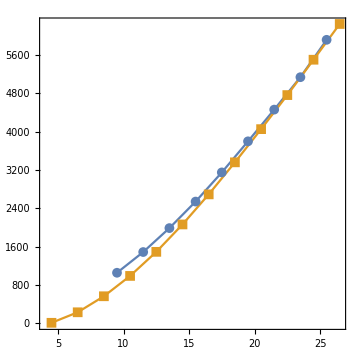

```mathematica
ListPlot[{t1n,t2n},Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Medium,Frame->True,Axes->False,AspectRatio->1]
```

## ^183Au - Negative Parity

```mathematica
x1p=Table[N[i],{i,13/2,65/2,2}];
y1p=Reverse[{7848,7103,6375,5677,4986,4308,3655,3049,2492,1983,1530,1151,867,702}];
t1p=Table[{x1p[[i]],y1p[[i]]},{i,1,Length[x1p]}];
```

```mathematica
x2p=Table[N[i],{i,23/2,43/2,2}];
y2p=Reverse[{4464,3840,3243,2684,2178,1739}];
t2p=Table[{x2p[[i]],y2p[[i]]},{i,1,Length[x2p]}];
```

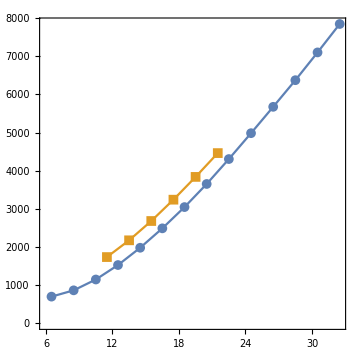

```mathematica
ListPlot[{t1p,t2p},Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Medium,Frame->True,Axes->False,AspectRatio->1]
```